# Vaje 6

3. 4. 2025

## 1. Naloga

a) Dana je funkcija . Definirajte funkcijo dveh spremenljivk.

b) Izračunajte gradient funkcije (par, kjer je na prvem mestu odvod funkcije po x in na drugem mestu odvod funkcije po y). Kdaj je gradient enak 0?

c) Definirajte Hessejevo matriko za funkcijo  in ugotovite, ali je v točki, kjer je gradient funkcije enak 0, dosežen lokalni ekstrem.

d) Narišite nivojnico  in označite kritične točke. Vrednost paramtera  naj bo moč spreminjati. Narišite tudi graf funkcije f in označite lokalni minimum.

```mathematica
(*kritične točke, pri 0, (1,1)*)
```

## 2. Naloga

Dana je enačba ploskve .

a) Poiščite precečišča te ploskve s koordinatnimi ravninami.

b) Narišite ploskev v 3D.

## 3. Naloga

Dana je funkcija .

a) Razvijte funkcijo v Taylorjev polinom stopnje 6 okoli točke 0.

```mathematica
f[x_] := E^x * Cos[x^3]
polinom = Normal[Series[f[x], {x, 0, 6}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120-(359 x^6)/720

b) Narišite originalno funkcijo in njeno aproksimacijo na intervalu [-2, 2].

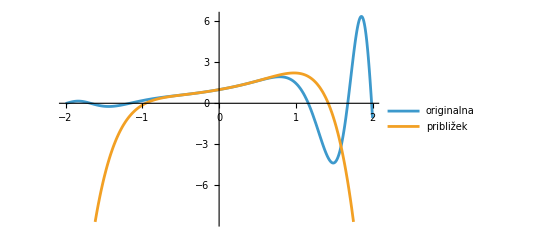

```mathematica
Plot[{f[x], polinom},{x, -2, 2}, PlotLegends->{"originalna", "približek"}]
```

## 4. Naloga

a) Aproksimiraj  s Taylorjevim polinomom stopnje 2 okoli x=0 in oceni napako, ki jo doiš kosinusc-1..neki tazga

```mathematica
priblizek = Normal[Series[Cos[x], {x,0,2}]]
```

1-x^2/2

```mathematica
pribliznaVrednost =priblizek /. {x -> 0.1}
```

0.995

```mathematica
razlika =Cos[0.1] -pribliznaVrednost
```

4.16528×10^-6

b) Uporabi Taylorjev polinom stopnje 3 za izračun približka .

```mathematica
priblizek[x_]:= Normal[Series[Log[x],{x,1,2}]] 
pribliznaVrednost = priblizek[1.1]
```

SetDelayed::write: Tag Plus in (1-x^2/2)[x_] is Protected.

$Failed

(1-x^2/2)[1.1]

## 5. Naloga

a) Poišči radij konvergence Tylorjeve vrste  okoli .

b) Določij konvergenčni polmer vrste .